# Escape time versus initial shooting angle for some values of b (part 2)

The escape time is defined as the time it takes for a particle to either be captured (ρ=1), or to escape to infinity (|ρcosθ | >z_crit). In our previous basin plots, z_crit was taken to be z_crit=1000. We stick with that definition. We are only interested in the regularity of the scattering function, not its actual value. In here we zoom in on a different set of regions of ϕ_sh.

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Equations of motion and orbital parameters

Our initial condition is the point (ρ,θ)=(3,π/2) and we assume that the particle is initially in a circular orbit. This restricts the value of l

```mathematica
l[b_]:=If[$IsPositive,-3b+√(3+144 b^2),-3b-√(3+144 b^2)];
```

This also restricts the value of U_eff.

```mathematica
Ueff[b_]:=(1-1/3)(1+(l[b]-9b )^2/9);
```

The equations of motion are

```mathematica
ddrho[b_] := ρ''[σ]==1/2(2ρ[σ]-3)(θ'[σ])^2+(2l[b]b-1)/(2 ρ[σ]^2)+(l[b]^2(2ρ[σ]-3))/(2 ρ[σ]^4 Sin[θ[σ]]^2)-b^2/2(2ρ[σ]-1)Sin[θ[σ]]^2
ddθ[b_]:= θ''[σ]==-2/ρ[σ]ρ'[σ]θ'[σ]+(l[b]^2 Cos[θ[σ]])/(ρ[σ]^4 Sin[θ[σ]]^3)-b^2 Sin[θ[σ]]Cos[θ[σ]]
```

To obtain the initial conditions (ρ'[0],θ'[0]) we use the function below. The angle ϕ_sh is taken with respect to the positive z axis, where clockwise correspond to positive ϕ_sh.

```mathematica
getVelocities[b_,en_,ϕsh_]:=Module[{dρ0,dθ0,result},
dρ0=(√((en^2-Ueff[b])/(Sin[ϕsh]^2+6 Cos[ϕsh]^2)))Sin[ϕsh];
dθ0=-(√((en^2-Ueff[b])/(Sin[ϕsh]^2+6 Cos[ϕsh]^2)))Cos[ϕsh];
result={dρ0,dθ0}
];
```

## The scattering function

We need a function that takes as its input ϕ_sh and outputs the escape time T_e:

```mathematica
(*It seems that for a WorkingPrecision of 25, the error is on the order of ~10^-8 (see ErrorScratch).*)
TEscape[b_,en_,ϕsh_]:=Module[{initVelocities,escTime},
escTime=MaximumT+1;
initVelocities=getVelocities[b,en,ϕsh];
Quiet@NDSolve[{ddrho[b],ddθ[b],ρ[0]==3,ρ'[0]==initVelocities⟦1⟧,θ[0]==π/2,θ'[0]==initVelocities⟦2⟧,WhenEvent[Abs[ρ[σ]Cos[θ[σ]]]>1000,escTime=σ;"StopIntegration"],WhenEvent[ρ[σ]≤1,escTime=σ;"StopIntegration"]},{ρ,θ},{σ,0,MaximumT+1},WorkingPrecision->25,MaxSteps->∞];
Return[escTime]
]; 
(* If we want to zoom in on values, perhaps we need to increase the WorkingPrecision. With this, TEscape has an optional argument to control the Working Precision (default value 25).*)
TEscape[b_,en_,ϕsh_,wPrec_]:=Module[{initVelocities,escTime},
escTime=MaximumT+1;
initVelocities=getVelocities[b,en,ϕsh];
Quiet@NDSolve[{ddrho[b],ddθ[b],ρ[0]==3,ρ'[0]==initVelocities⟦1⟧,θ[0]==π/2,θ'[0]==initVelocities⟦2⟧,WhenEvent[Abs[ρ[σ]Cos[θ[σ]]]>1000,escTime=σ;"StopIntegration"],WhenEvent[ρ[σ]≤1,escTime=σ;"StopIntegration"]},{ρ,θ},{σ,0,MaximumT+1},WorkingPrecision->wPrec,MaxSteps->∞];
Return[escTime]
];
```

## Other parameters

Here we set the maximum integration time, and number of trajectories that we will integrate. We will also launch additional kernels

```mathematica
MaximumT=10^6;numTrajectories=1000;shootAngles=Subdivide[-π,π,numTrajectories-1];
LaunchKernels[6];
SetSharedVariable[Progress,trajCount];
```

```mathematica
$KernelCount
```

6

## Positive l

```mathematica
$IsPositive=True;
```

## ε=1.2

```mathematica
ε=1.2;
```

### We zoom in at ϕ_sh∈(1,2)

```mathematica
b=0.1;
```

```mathematica
Progress=0;trajCount=0;shootAngleszoom=Subdivide[1,2,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData1=Transpose[{shootAngleszoom,rawData}];
Export["pl_b(01)_e(12)_phi(1_2).mx",finalData1]
```

{614.094,Null}

pl_b(01)_e(12)_phi(1_2).mx

```mathematica
b=0.5;
```

```mathematica
Progress=0;trajCount=0;shootAngleszoom=Subdivide[1,2,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData2=Transpose[{shootAngleszoom,rawData}];
Export["pl_b(05)_e(12)_phi(1_2).mx",finalData2]
```

{3118.37,Null}

pl_b(05)_e(12)_phi(1_2).mx

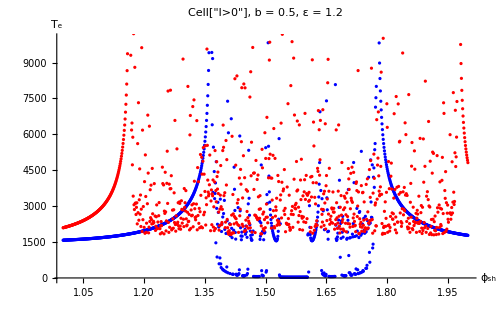

```mathematica
plot=ListPlot[{finalData1,finalData2},PlotRange->{All,{0,10000}},PlotStyle->{Blue,Red},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"b35c35df-7ebc-4650-ba2a-922fedd7ac66"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

### We zoom in further at ϕ_sh∈(1.5,1.7)

```mathematica
b=0.1;Progress=0;trajCount=0;shootAngleszoom=Subdivide[1.5,1.7,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData1=Transpose[{shootAngleszoom,rawData}];
Export["pl_b(01)_e(12)_phi(15_17).mx",finalData1]
```

{347.295,Null}

pl_b(01)_e(12)_phi(15_17).mx

```mathematica
b=0.5;Progress=0;trajCount=0;shootAngleszoom=Subdivide[1.5,1.7,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData2=Transpose[{shootAngleszoom,rawData}];
Export["pl_b(05)_e(12)_phi(15_17).mx",finalData2]
```

{3191.89,Null}

pl_b(05)_e(12)_phi(15_17).mx

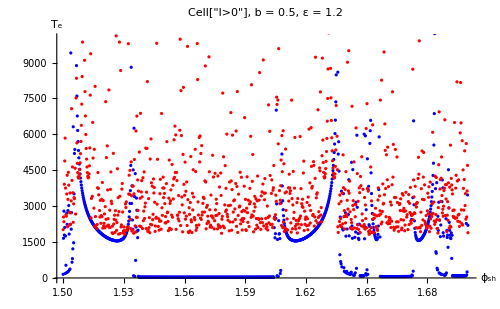

```mathematica
plot=ListPlot[{finalData1,finalData2},PlotRange->{All,{0,10000}},PlotStyle->{Blue,Red},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"6da2b6cf-97c9-483a-813a-57eb8bf679da"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

### We zoom in further at ϕ_sh∈(1.57,1.58)

```mathematica
b=0.1;Progress=0;trajCount=0;shootAngleszoom=Subdivide[1.57,1.58,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData1=Transpose[{shootAngleszoom,rawData}];
Export["pl_b(01)_e(12)_phi(157_158).mx",finalData1]
```

{21.232,Null}

pl_b(01)_e(12)_phi(157_158).mx

```mathematica
b=0.5;Progress=0;trajCount=0;shootAngleszoom=Subdivide[1.57,1.58,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData2=Transpose[{shootAngleszoom,rawData}];
Export["pl_b(05)_e(12)_phi(157_158).mx",finalData2]
```

{3208.77,Null}

pl_b(05)_e(12)_phi(157_158).mx

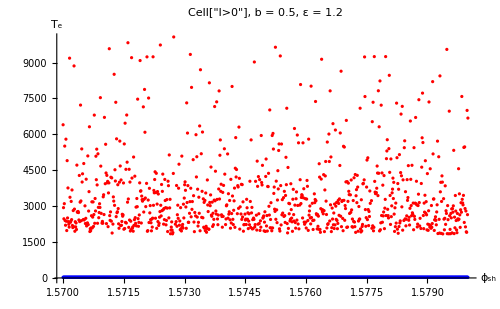

```mathematica
plot=ListPlot[{finalData1,finalData2},PlotRange->{All,{0,10000}},PlotStyle->{Blue,Red},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"150f70d2-029e-470c-b430-13b68cf57a8e"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

### We zoom in at ϕ_sh∈(-3,-2)

```mathematica
b=0.1;Progress=0;trajCount=0;shootAngleszoom=Subdivide[-3,-2,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData1=Transpose[{shootAngleszoom,rawData}];
Export["pl_b(01)_e(12)_phi(-3_-2).mx",finalData1]
```

{791.281,Null}

pl_b(01)_e(12)_phi(-3_-2).mx

```mathematica
b=0.5;Progress=0;trajCount=0;shootAngleszoom=Subdivide[-3,-2,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData2=Transpose[{shootAngleszoom,rawData}];
Export["pl_b(05)_e(12)_phi(-3_-2).mx",finalData2]
```

{3152.54,Null}

pl_b(05)_e(12)_phi(-3_-2).mx

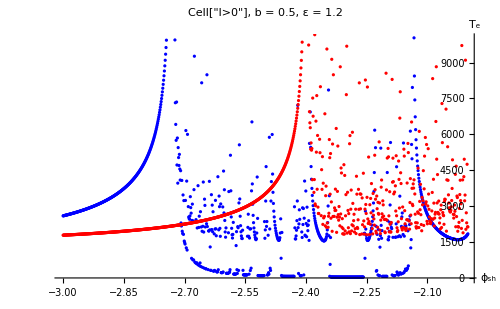

```mathematica
plot=ListPlot[{finalData1,finalData2},PlotRange->{All,{0,10000}},PlotStyle->{Blue,Red},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"7ff3b3e0-7098-4f34-98ba-89addab1f737"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

### We zoom in further at ϕ_sh∈(-2.4,-2.2)

```mathematica
b=0.1;Progress=0;trajCount=0;shootAngleszoom=Subdivide[-2.4,-2.2,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData1=Transpose[{shootAngleszoom,rawData}];
Export["pl_b(01)_e(12)_phi(-24_-22).mx",finalData1]
```

{489.082,Null}

pl_b(01)_e(12)_phi(-24_-22).mx

```mathematica
b=0.5;Progress=0;trajCount=0;shootAngleszoom=Subdivide[-2.4,-2.2,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData2=Transpose[{shootAngleszoom,rawData}];
Export["pl_b(05)_e(12)_phi(-24_-22).mx",finalData2]
```

{4207.9,Null}

pl_b(05)_e(12)_phi(-24_-22).mx

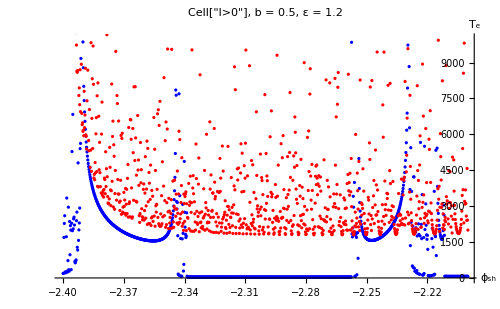

```mathematica
plot=ListPlot[{finalData1,finalData2},PlotRange->{All,{0,10000}},PlotStyle->{Blue,Red},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"1f0d8324-d222-41de-8af8-e657bbafd65b"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

### We zoom in further at ϕ_sh∈(-2.25,-2.23)

```mathematica
b=0.1;Progress=0;trajCount=0;shootAngleszoom=Subdivide[-2.25,-2.23,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData1=Transpose[{shootAngleszoom,rawData}];
Export["pl_b(01)_e(12)_phi(-225_-223).mx",finalData1]
```

{561.329,Null}

pl_b(01)_e(12)_phi(-225_-223).mx

```mathematica
b=0.5;Progress=0;trajCount=0;shootAngleszoom=Subdivide[-2.25,-2.23,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData2=Transpose[{shootAngleszoom,rawData}];
Export["pl_b(05)_e(12)_phi(-225_-223).mx",finalData2]
```

{3042.02,Null}

pl_b(05)_e(12)_phi(-225_-223).mx

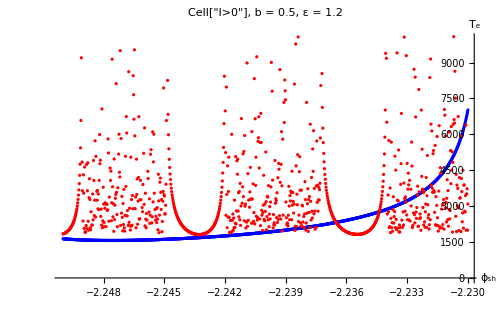

```mathematica
plot=ListPlot[{finalData1,finalData2},PlotRange->{All,{0,10000}},PlotStyle->{Blue,Red},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"ccf38b87-2a87-4a4f-bff8-2f54cbc9eabb"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

## ε=3

```mathematica
ε=3;
```

### We zoom in at ϕ_sh∈(1.2,1.8)

```mathematica
b=0.1;Progress=0;trajCount=0;shootAngleszoom=Subdivide[1.2,1.8,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData1=Transpose[{shootAngleszoom,rawData}];
Export["pl_b(01)_e(30)_phi(12_18).mx",finalData1]
```

{627.377,Null}

pl_b(01)_e(30)_phi(12_18).mx

```mathematica
b=0.5;Progress=0;trajCount=0;shootAngleszoom=Subdivide[1.2,1.8,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData2=Transpose[{shootAngleszoom,rawData}];
Export["pl_b(05)_e(30)_phi(12_18).mx",finalData2]
```

{1032.76,Null}

pl_b(05)_e(30)_phi(12_18).mx

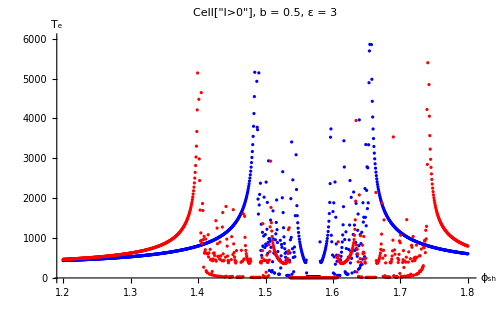

```mathematica
plot=ListPlot[{finalData1,finalData2},PlotRange->{All,{0,6000}},PlotStyle->{Blue,Red},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"6e59b567-e234-471e-813b-52c504219ff6"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

### We zoom in further at ϕ_sh∈(1.52,1.62)

```mathematica
b=0.1;Progress=0;trajCount=0;shootAngleszoom=Subdivide[1.52,1.62,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData1=Transpose[{shootAngleszoom,rawData}];
Export["pl_b(01)_e(30)_phi(152_162).mx",finalData1]
```

{498.807,Null}

pl_b(01)_e(30)_phi(152_162).mx

```mathematica
b=0.5;Progress=0;trajCount=0;shootAngleszoom=Subdivide[1.52,1.62,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData2=Transpose[{shootAngleszoom,rawData}];
Export["pl_b(05)_e(30)_phi(152_162).mx",finalData2]
```

{195.269,Null}

pl_b(05)_e(30)_phi(152_162).mx

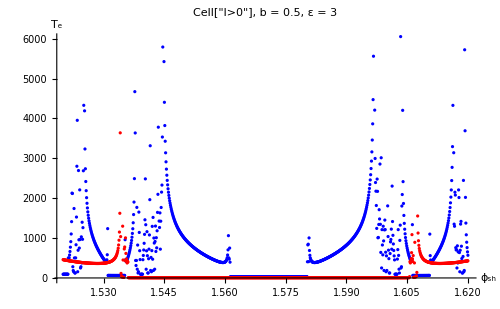

```mathematica
plot=ListPlot[{finalData1,finalData2},PlotRange->{All,{0,6000}},PlotStyle->{Blue,Red},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"3ff5beb1-30c0-45b6-81f2-0e1e4e625207"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

### We zoom in further at ϕ_sh∈(1.4,1.5)

```mathematica
b=0.1;Progress=0;trajCount=0;shootAngleszoom=Subdivide[1.4,1.5,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData1=Transpose[{shootAngleszoom,rawData}];
Export["pl_b(01)_e(30)_phi(140_150).mx",finalData1]
```

{1034.23,Null}

pl_b(01)_e(30)_phi(140_150).mx

```mathematica
b=0.5;Progress=0;trajCount=0;shootAngleszoom=Subdivide[1.4,1.5,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData2=Transpose[{shootAngleszoom,rawData}];
Export["pl_b(05)_e(30)_phi(140_150).mx",finalData2]
```

{1003.12,Null}

pl_b(05)_e(30)_phi(140_150).mx

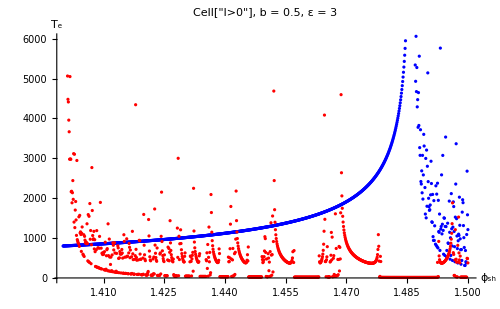

```mathematica
plot=ListPlot[{finalData1,finalData2},PlotRange->{All,{0,6000}},PlotStyle->{Blue,Red},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"69717c59-97f5-4ab8-94dd-7fbeb816193c"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

### We zoom in at ϕ_sh∈(-2.6,-2.2)

```mathematica
b=0.1;Progress=0;trajCount=0;shootAngleszoom=Subdivide[-2.6,-2.2,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData1=Transpose[{shootAngleszoom,rawData}];
Export["pl_b(01)_e(30)_phi(-26_-22).mx",finalData1]
```

{789.642,Null}

pl_b(01)_e(30)_phi(-26_-22).mx

```mathematica
b=0.5;Progress=0;trajCount=0;shootAngleszoom=Subdivide[-2.6,-2.2,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData2=Transpose[{shootAngleszoom,rawData}];
Export["pl_b(05)_e(30)_phi(-26_-22).mx",finalData2]
```

{1626.95,Null}

pl_b(05)_e(30)_phi(-26_-22).mx

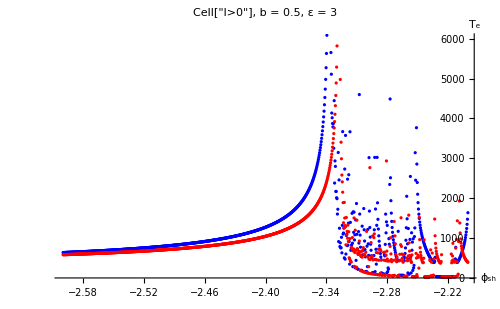

```mathematica
plot=ListPlot[{finalData1,finalData2},PlotRange->{All,{0,6000}},PlotStyle->{Blue,Red},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"2d4284d5-6464-4cf8-9a99-53d2624c6339"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

### We zoom further at in at ϕ_sh∈(-2.32,-2.24)

```mathematica
b=0.1;Progress=0;trajCount=0;shootAngleszoom=Subdivide[-2.32,-2.24,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData1=Transpose[{shootAngleszoom,rawData}];
Export["pl_b(01)_e(30)_phi(-232_-224).mx",finalData1]
```

{764.168,Null}

pl_b(01)_e(30)_phi(-232_-224).mx

```mathematica
b=0.5;Progress=0;trajCount=0;shootAngleszoom=Subdivide[-2.32,-2.24,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData2=Transpose[{shootAngleszoom,rawData}];
Export["pl_b(05)_e(30)_phi(-232_-224).mx",finalData2]
```

{967.093,Null}

pl_b(05)_e(30)_phi(-232_-224).mx

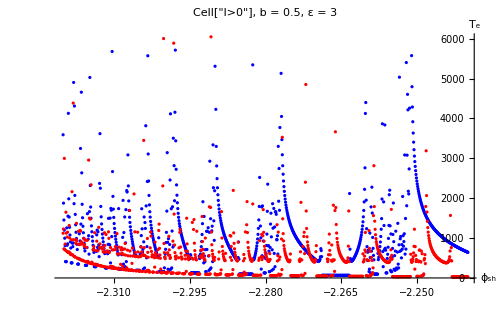

```mathematica
plot=ListPlot[{finalData1,finalData2},PlotRange->{All,{0,6000}},PlotStyle->{Blue,Red},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"985ca3b6-4b71-4de7-9724-212756ea8e00"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

## Negative l

```mathematica
$IsPositive=False;
εcrit[b_]:=√(1+4 b Abs[l[b]]);
```

## ε=ε_crit+0.2

### We zoom in at ϕ_sh∈(1,2)

```mathematica
b=0.01;ε=εcrit[b]+0.2;Progress=0;trajCount=0;shootAngleszoom=Subdivide[1,2,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData1=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(001)_e(crit_02)_phi(1_2).mx",finalData1]
```

{230.715,Null}

ml_b(001)_e(crit_02)_phi(1_2).mx

```mathematica
b=0.1;ε=εcrit[b]+0.2;Progress=0;trajCount=0;shootAngleszoom=Subdivide[1,2,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData2=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(01)_e(crit_02)_phi(1_2).mx",finalData2]
```

{537.768,Null}

ml_b(01)_e(crit_02)_phi(1_2).mx

```mathematica
b=0.5;ε=εcrit[b]+0.2;Progress=0;trajCount=0;shootAngleszoom=Subdivide[1,2,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData3=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(05)_e(crit_02)_phi(1_2).mx",finalData3]
```

{895.383,Null}

ml_b(05)_e(crit_02)_phi(1_2).mx

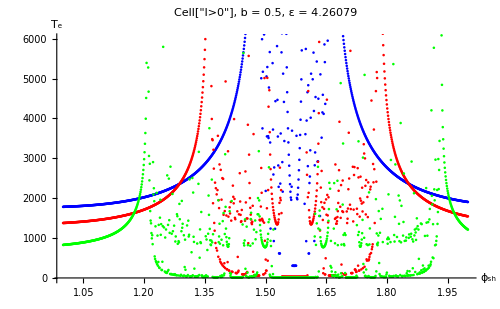

```mathematica
plot=ListPlot[{finalData1,finalData2,finalData3},PlotRange->{All,{0,6000}},PlotStyle->{Blue,Red,Green},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"2c2df35a-2a4a-4cab-ade7-7b2ece18a0e7"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

### We further zoom in at ϕ_sh∈(1.5,1.65)

```mathematica
b=0.01;ε=εcrit[b]+0.2;Progress=0;trajCount=0;shootAngleszoom=Subdivide[1.5,1.65,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData1=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(001)_e(crit_02)_phi(15_165).mx",finalData1]
```

{415.584,Null}

ml_b(001)_e(crit_02)_phi(15_165).mx

```mathematica
b=0.1;ε=εcrit[b]+0.2;Progress=0;trajCount=0;shootAngleszoom=Subdivide[1.5,1.65,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData2=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(01)_e(crit_02)_phi(15_165).mx",finalData2]
```

{370.417,Null}

ml_b(01)_e(crit_02)_phi(15_165).mx

```mathematica
b=0.5;ε=εcrit[b]+0.2;Progress=0;trajCount=0;shootAngleszoom=Subdivide[1.5,1.65,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData3=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(05)_e(crit_02)_phi(15_165).mx",finalData3]
```

{266.523,Null}

ml_b(05)_e(crit_02)_phi(15_165).mx

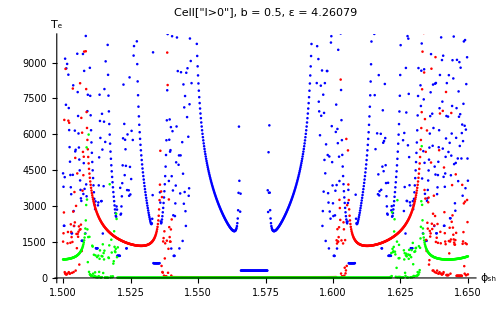

```mathematica
plot=ListPlot[{finalData1,finalData2,finalData3},PlotRange->{All,{0,10000}},PlotStyle->{Blue,Red,Green},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"bcb2a552-701d-43a6-81a2-432d343350cf"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

### We zoom in at ϕ_sh∈(-3,-2)

```mathematica
b=0.01;ε=εcrit[b]+0.2;Progress=0;trajCount=0;shootAngleszoom=Subdivide[-3,-2,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData1=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(001)_e(crit_02)_phi(-3_-2).mx",finalData1]
```

{373.569,Null}

ml_b(001)_e(crit_02)_phi(-3_-2).mx

```mathematica
b=0.1;ε=εcrit[b]+0.2;Progress=0;trajCount=0;shootAngleszoom=Subdivide[-3,-2,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData2=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(01)_e(crit_02)_phi(-3_-2).mx",finalData2]
```

{678.532,Null}

ml_b(01)_e(crit_02)_phi(-3_-2).mx

```mathematica
b=0.5;ε=εcrit[b]+0.2;Progress=0;trajCount=0;shootAngleszoom=Subdivide[-3,-2,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData3=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(05)_e(crit_02)_phi(-3_-2).mx",finalData3]
```

{621.817,Null}

ml_b(05)_e(crit_02)_phi(-3_-2).mx

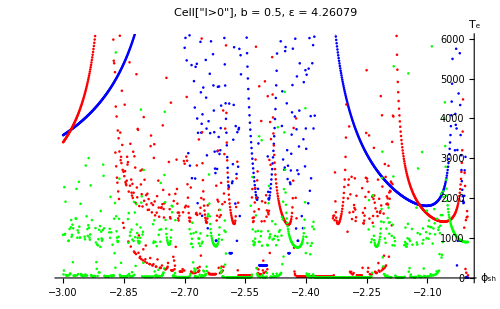

```mathematica
plot=ListPlot[{finalData1,finalData2,finalData3},PlotRange->{All,{0,6000}},PlotStyle->{Blue,Red,Green},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"ab0b706c-1e92-4677-b37c-cc86f5a8271e"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

### We further zoom in at ϕ_sh∈(-2.7,-2.55)

```mathematica
b=0.01;ε=εcrit[b]+0.2;Progress=0;trajCount=0;shootAngleszoom=Subdivide[-2.7,-2.55,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData1=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(001)_e(crit_02)_phi(-27_-255).mx",finalData1]
```

{481.502,Null}

ml_b(001)_e(crit_02)_phi(-27_-255).mx

```mathematica
b=0.1;ε=εcrit[b]+0.2;Progress=0;trajCount=0;shootAngleszoom=Subdivide[-2.7,-2.55,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData2=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(01)_e(crit_02)_phi(-27_-255).mx",finalData2]
```

{434.592,Null}

ml_b(01)_e(crit_02)_phi(-27_-255).mx

```mathematica
b=0.5;ε=εcrit[b]+0.2;Progress=0;trajCount=0;shootAngleszoom=Subdivide[-2.7,-2.55,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData3=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(05)_e(crit_02)_phi(-27_-255).mx",finalData3]
```

{628.116,Null}

ml_b(05)_e(crit_02)_phi(-27_-255).mx

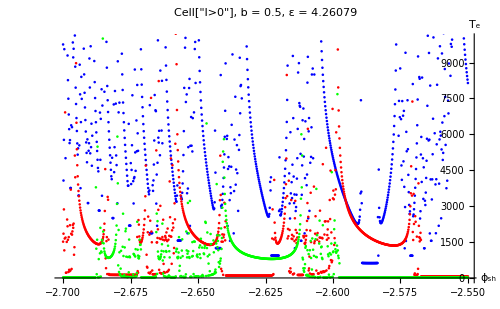

```mathematica
plot=ListPlot[{finalData1,finalData2,finalData3},PlotRange->{All,{0,10000}},PlotStyle->{Blue,Red,Green},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"0a6bf65b-fcc5-4a63-9991-a87649c774ce"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

## ε=ε_crit+2

### We zoom in at ϕ_sh∈(1.2,2)

```mathematica
b=0.01;ε=εcrit[b]+2;Progress=0;trajCount=0;shootAngleszoom=Subdivide[1.2,2,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData1=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(001)_e(crit_2)_phi(12_2).mx",finalData1]
```

{144.744,Null}

ml_b(001)_e(crit_2)_phi(12_2).mx

```mathematica
b=0.1;ε=εcrit[b]+2;Progress=0;trajCount=0;shootAngleszoom=Subdivide[1.2,2,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData2=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(01)_e(crit_2)_phi(12_2).mx",finalData2]
```

{496.125,Null}

ml_b(01)_e(crit_2)_phi(12_2).mx

```mathematica
b=0.5;ε=εcrit[b]+2;Progress=0;trajCount=0;shootAngleszoom=Subdivide[1.2,2,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData3=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(05)_e(crit_2)_phi(12_2).mx",finalData3]
```

{765.583,Null}

ml_b(05)_e(crit_2)_phi(12_2).mx

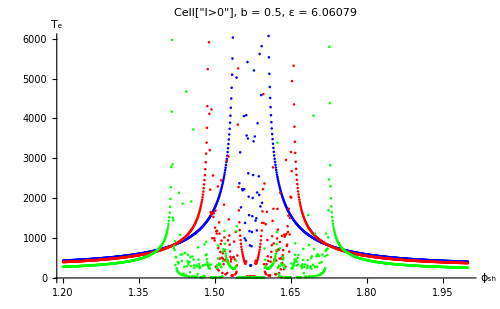

```mathematica
plot=ListPlot[{finalData1,finalData2,finalData3},PlotRange->{All,{0,6000}},PlotStyle->{Blue,Red,Green},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"f9025346-3876-4a5d-a0b6-83014186b33e"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

### We further zoom in at ϕ_sh∈(1.5,1.65)

```mathematica
b=0.01;ε=εcrit[b]+2;Progress=0;trajCount=0;shootAngleszoom=Subdivide[1.5,1.65,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData1=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(001)_e(crit_2)_phi(15_165).mx",finalData1]
```

{487.889,Null}

ml_b(001)_e(crit_2)_phi(15_165).mx

```mathematica
b=0.1;ε=εcrit[b]+2;Progress=0;trajCount=0;shootAngleszoom=Subdivide[1.5,1.65,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData2=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(01)_e(crit_2)_phi(15_165).mx",finalData2]
```

{621.816,Null}

ml_b(01)_e(crit_2)_phi(15_165).mx

```mathematica
b=0.5;ε=εcrit[b]+2;Progress=0;trajCount=0;shootAngleszoom=Subdivide[1.5,1.65,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData3=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(05)_e(crit_2)_phi(15_165).mx",finalData3]
```

{423.11,Null}

ml_b(05)_e(crit_2)_phi(15_165).mx

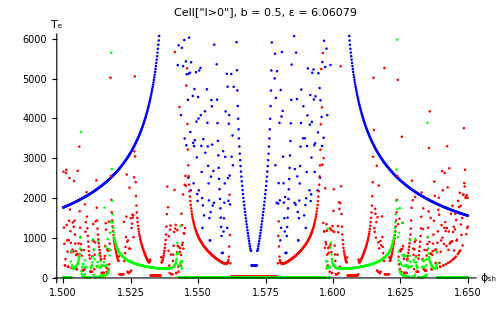

```mathematica
plot=ListPlot[{finalData1,finalData2,finalData3},PlotRange->{All,{0,6000}},PlotStyle->{Blue,Red,Green},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"1161fe4b-ff21-401f-96e6-b9c2eb2c7124"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

### We zoom in at ϕ_sh∈(-2.8,-2)

```mathematica
b=0.01;ε=εcrit[b]+2;Progress=0;trajCount=0;shootAngleszoom=Subdivide[-2.8,-2,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData1=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(001)_e(crit_2)_phi(-28_-2).mx",finalData1]
```

{178.215,Null}

ml_b(001)_e(crit_2)_phi(-28_-2).mx

```mathematica
b=0.1;ε=εcrit[b]+2;Progress=0;trajCount=0;shootAngleszoom=Subdivide[-2.8,-2,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData2=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(01)_e(crit_2)_phi(-28_-2).mx",finalData2]
```

{585.236,Null}

ml_b(01)_e(crit_2)_phi(-28_-2).mx

```mathematica
b=0.5;ε=εcrit[b]+2;Progress=0;trajCount=0;shootAngleszoom=Subdivide[-2.8,-2,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData3=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(05)_e(crit_2)_phi(-28_-2).mx",finalData3]
```

{919.794,Null}

ml_b(05)_e(crit_2)_phi(-28_-2).mx

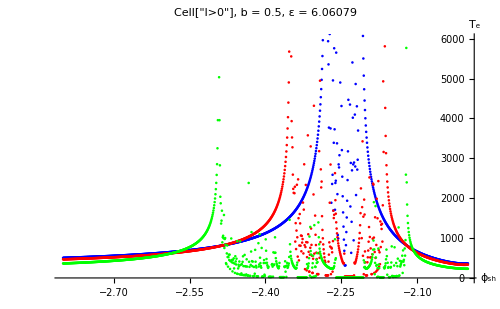

```mathematica
plot=ListPlot[{finalData1,finalData2,finalData3},PlotRange->{All,{0,6000}},PlotStyle->{Blue,Red,Green},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"f7ae429e-b612-4d74-8213-c3b86b7dbcef"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

### We further zoom in at ϕ_sh∈(-2.3,-2.2)

```mathematica
b=0.01;ε=εcrit[b]+2;Progress=0;trajCount=0;shootAngleszoom=Subdivide[-2.3,-2.2,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData1=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(001)_e(crit_2)_phi(-23_-22).mx",finalData1]
```

{677.381,Null}

ml_b(001)_e(crit_2)_phi(-23_-22).mx

```mathematica
b=0.1;ε=εcrit[b]+2;Progress=0;trajCount=0;shootAngleszoom=Subdivide[-2.3,-2.2,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData2=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(01)_e(crit_2)_phi(-23_-22).mx",finalData2]
```

{492.747,Null}

ml_b(01)_e(crit_2)_phi(-23_-22).mx

```mathematica
b=0.5;ε=εcrit[b]+2;Progress=0;trajCount=0;shootAngleszoom=Subdivide[-2.3,-2.2,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData3=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(05)_e(crit_2)_phi(-23_-22).mx",finalData3]
```

{360.79,Null}

ml_b(05)_e(crit_2)_phi(-23_-22).mx

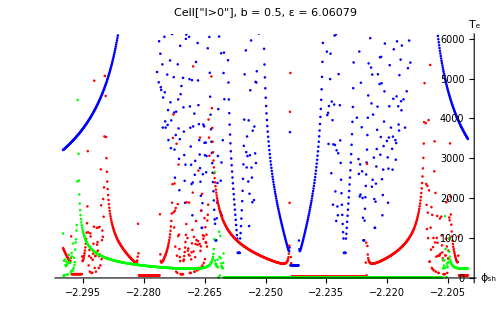

```mathematica
plot=ListPlot[{finalData1,finalData2,finalData3},PlotRange->{All,{0,6000}},PlotStyle->{Blue,Red,Green},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"6e66772e-f390-46b7-9f99-021b00fc76c0"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```